```mathematica
$Line=-2;
ClearAll;
```

```mathematica
(* Pivot Function *)
pivot[iStar_, jStar_, m_] :=(
(* Create copy of matrix  and get dimensions *)
mm=m;
rows=Dimensions[m][[1]];
cols=Dimensions[m][[2]];
(* Begin Pivoting *)
mm[[1,jStar] ]=m[[iStar,cols]]; 
mm[[iStar,cols]]=m[[1,jStar]];
For[row=2, row≤rows, row++,
For[col=1,col<cols,col++,
{
(* P *)
If[row==iStar && col==jStar,
mm[[row,col]]=1/m[[iStar,jStar]]],
(* Q *)
If[row==iStar && col ≠ jStar,
mm[[row,col]]=-m[[row,col]]/m[[iStar, jStar]]],
(* R *)
If[row≠iStar && col== jStar,
mm[[row,col]]=m[[row,col]]/m[[iStar, jStar]]],
(* S *)
If[row≠iStar && col ≠ jStar,
mm[[row,col]]=m[[row,col]]-m[[iStar,col]]m[[row,jStar]]/m[[iStar,jStar]]]
}
]
];
Return[mm];
)
```

```mathematica
(* Quiz 04 *)
(* x1=u1-u2; x2=v1-v2; *)
(* Define function for objective *)
z[x1_,x2_] :=-2x1-4x2+4;

(* Define functions for constraints *)
g1[x1_,x2_] :=4x1+3x2 ;
g2[x1_,x2_] :=4x1+3x2;
g3[x1_,x2_] :=-3x1+x2 ;
g4[x1_,x2_] :=3x1-x2;
gm[x1_,x2_]:={g1[x1,x2],g2[x1,x2],g3[x1,x2],g4[x1,x2]}

(* Define functions for slack variables *)
s1f[x1_,x2_] :=-4x1-3x2+48;
s2f[x1_,x2_]:=4x1+3x2-24;
s3f[x1_,x2_]:=3x1-x2+6;
s4f[x1_,x2_] :=-3x1+x2+6;
sm[x1_,x2_]:={s1f[x1,x2],s2f[x1,x2],s3f[x1,x2],s4f[x1,x2]}

(* Create Tableaux *)
m0={x1,x2,1,""};
m1={-4,-3,48,s1};
m2={4,3,-24,s2};
m3={3,-1,6,s3};
m4={-3,1,6,s4};
mobj={-2,-4,4,-z->min};
t0={m0,m1,m2,m3,m4,mobj};
```

t0=(x1 | x2 | 1 | 
-4 | -3 | 48 | s1
4 | 3 | -24 | s2
3 | -1 | 6 | s3
-3 | 1 | 6 | s4
-2 | -4 | 4 | -z→min)

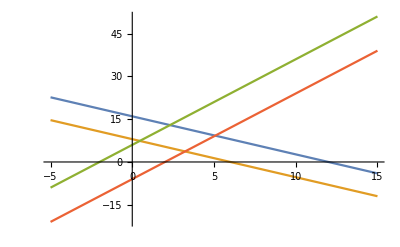

```mathematica
Print["t0=",MatrixForm[t0]]
Plot[{-4/3x1+16,-4/3x1+8,3x1+6,3x1-6}, {x1,-5, 15}]
```

```mathematica
(* T1 *)
t1=pivot[4,1,t0];
x1t1=t1[[4,3]];
x2t1=0;
Print["t1=",MatrixForm[t1]]
Print["x1_t1=", x1t1//N]
Print["x2_t1=", x2t1//N]
Print["S_t1=",MatrixForm[sm[x1t1,x2t1]]//N]
Print["z_t1=", z[x1t1,x2t1]//N]
```

t1=(s3 | x2 | 1 | 
-4/3 | -13/3 | 56 | s1
4/3 | 13/3 | -32 | s2
1/3 | 1/3 | -2 | x1
-1 | 0 | 12 | s4
-2/3 | -14/3 | 8 | -z→min)

x1_t1=-2.

x2_t1=0.

S_t1=(56.
-32.
0.
12.)

z_t1=8.

```mathematica
(* T2 *)
t2=pivot[3,2,t1];
x1t2=t2[[4,3]];
x2t2=t2[[3,3]];
Print["t2=",MatrixForm[t2]]
Print["x1_t2=", x1t2//N]
Print["x2_t2=", x2t2//N]
Print["S_t2=",MatrixForm[sm[x1t2,x2t2]]//N]
Print["z_t2=", z[x1t2,x2t2]//N]
```

t2=(s3 | s2 | 1 | 
0 | -1 | 24 | s1
-4/13 | 3/13 | 96/13 | x2
3/13 | 1/13 | 6/13 | x1
-1 | 0 | 12 | s4
10/13 | -14/13 | -344/13 | -z→min)

x1_t2=0.461538

x2_t2=7.38462

S_t2=(24.
0.
0.
12.)

z_t2=-26.4615

```mathematica
(* T3 *)
t3=pivot[2,2,t2];
x1t3=t3[[4,3]];
x2t3=t3[[3,3]];
Print["t3=",MatrixForm[t3]]
Print["x1_t3=", x1t3//N]
Print["x2_t3=", x2t3//N]
Print["S_t3=",MatrixForm[sm[x1t3,x2t3]]//N]
Print["z_t3=", z[x1t3,x2t3]//N]
```

t3=(s3 | s1 | 1 | 
0 | -1 | 24 | s2
-4/13 | -3/13 | 168/13 | x2
3/13 | -1/13 | 30/13 | x1
-1 | 0 | 12 | s4
10/13 | 14/13 | -680/13 | -z→min)

x1_t3=2.30769

x2_t3=12.9231

S_t3=(0.
24.
0.
12.)

z_t3=-52.3077

```mathematica
(* T4 *)
t4=pivot[5,1,t3];
x1t4=t4[[4,3]];
x2t4=t4[[3,3]];
Print["t4=",MatrixForm[t4]]
Print["x1_t4=", x1t4//N]
Print["x2_t4=", x2t4//N]
Print["S_t4=",MatrixForm[sm[x1t4,x2t4]]//N]
Print["z_t4=", z[x1t4,x2t4]//N]
```

t4=(s4 | s1 | 1 | 
0 | -1 | 24 | s2
4/13 | -3/13 | 120/13 | x2
-3/13 | -1/13 | 66/13 | x1
-1 | 0 | 12 | s3
-10/13 | 14/13 | -560/13 | -z→min)

x1_t4=5.07692

x2_t4=9.23077

S_t4=(0.
24.
12.
0.)

z_t4=-43.0769

```mathematica
(* T5 *)
t5=pivot[2,2,t4];
x1t5=t5[[4,3]];
x2t5=t5[[3,3]];
Print["t5=",MatrixForm[t5]]
Print["x1_t5=", x1t5//N]
Print["x2_t5=", x2t5//N]
Print["S_t5=",MatrixForm[sm[x1t5,x2t5]]//N]
Print["z_t5=", z[x1t5,x2t5]//N]
```

t5=(s4 | s2 | 1 | 
0 | -1 | 24 | s1
4/13 | 3/13 | 48/13 | x2
-3/13 | 1/13 | 42/13 | x1
-1 | 0 | 12 | s3
-10/13 | -14/13 | -224/13 | -z→min)

x1_t5=3.23077

x2_t5=3.69231

S_t5=(24.
0.
12.
0.)

z_t5=-17.2308

```mathematica
(* T6 *)
t6=pivot[3,1,t5];
x1t6=t6[[4,3]];
x2t6=0;
Print["t6=",MatrixForm[t6]]
Print["x1_t6=", x1t6//N]
Print["x2_t6=", x2t6//N]
Print["S_t6=",MatrixForm[sm[x1t6,x2t6]]//N]
Print["z_t6=", z[x1t6,x2t6]//N]
```

t6=(x2 | s2 | 1 | 
0 | -1 | 24 | s1
13/4 | -3/4 | -12 | s4
-3/4 | 1/4 | 6 | x1
-13/4 | 3/4 | 24 | s3
-5/2 | -1/2 | -8 | -z→min)

x1_t6=6.

x2_t6=0.

S_t6=(24.
0.
24.
-12.)

z_t6=-8.

```mathematica
(* T7 *)
t7=pivot[3,2,t6];
x1t7=t7[[4,3]];
x2t7=0;
Print["t7=",MatrixForm[t7]]
Print["x1_t7=", x1t7//N]
Print["x2_t7=", x2t7//N]
Print["S_t7=",MatrixForm[sm[x1t7,x2t7]]//N]
Print["z_t7=", z[x1t7,x2t7]//N]
```

t7=(x2 | s4 | 1 | 
-13/3 | 4/3 | 40 | s1
13/3 | -4/3 | -16 | s2
1/3 | -1/3 | 2 | x1
0 | -1 | 12 | s3
-14/3 | 2/3 | 0 | -z→min)

x1_t7=2.

x2_t7=0.

S_t7=(40.
-16.
12.
0.)

z_t7=0.

```mathematica
(* T8 *)
t8=pivot[2,2,t7];
x1t8=t8[[4,3]];
x2t8=0;
Print["t8=",MatrixForm[t8]]
Print["x1_t8=", x1t8//N]
Print["x2_t8=", x2t8//N]
Print["S_t8=",MatrixForm[sm[x1t8,x2t8]]//N]
Print["z_t8=", z[x1t8,x2t8]//N]
```

t8=(x2 | s1 | 1 | 
13/4 | 3/4 | -30 | s4
0 | -1 | 24 | s2
-3/4 | -1/4 | 12 | x1
-13/4 | -3/4 | 42 | s3
-5/2 | 1/2 | -20 | -z→min)

x1_t8=12.

x2_t8=0.

S_t8=(0.
24.
42.
-30.)

z_t8=-20.

```mathematica
(* T9 *)
t9=pivot[4,1,t8];
x1t9=0;
x2t9=t9[[4,3]];
Print["t9=",MatrixForm[t9]]
Print["x1_t9=", x1t9//N]
Print["x2_t9=", x2t9//N]
Print["S_t9=",MatrixForm[sm[x1t9,x2t9]]//N]
Print["z_t9=", z[x1t9,x2t9]//N]
```

t9=(x1 | s1 | 1 | 
-13/3 | -1/3 | 22 | s4
0 | -1 | 24 | s2
-4/3 | -1/3 | 16 | x2
13/3 | 1/3 | -10 | s3
10/3 | 4/3 | -60 | -z→min)

x1_t9=0.

x2_t9=16.

S_t9=(0.
24.
-10.
22.)

z_t9=-60.

```mathematica
(* T10 *)
t10=pivot[3,2,t9];
x1t10=0;
x2t10=t10[[4,3]];
Print["t10=",MatrixForm[t10]]
Print["x1_t10=", x1t10//N]
Print["x2_t10=", x2t10//N]
Print["S_t10=",MatrixForm[sm[x1t10,x2t10]]//N]
Print["z_t10=", z[x1t10,x2t10]//N]
```

t10=(x1 | s2 | 1 | 
-13/3 | 1/3 | 14 | s4
0 | -1 | 24 | s1
-4/3 | 1/3 | 8 | x2
13/3 | -1/3 | -2 | s3
10/3 | -4/3 | -28 | -z→min)

x1_t10=0.

x2_t10=8.

S_t10=(24.
0.
-2.
14.)

z_t10=-28.

```mathematica
(* T11 *)
t11=pivot[2,2,t10];
x1t11=0;
x2t11=t11[[4,3]];
Print["t11=",MatrixForm[t11]]
Print["x1_t11=", x1t11//N]
Print["x2_t11=", x2t11//N]
Print["S_t11=",MatrixForm[sm[x1t11,x2t11]]//N]
Print["z_t11=", z[x1t11,x2t11]//N]
```

t11=(x1 | s4 | 1 | 
13 | 3 | -42 | s2
-13 | -3 | 66 | s1
3 | 1 | -6 | x2
0 | -1 | 12 | s3
-14 | -4 | 28 | -z→min)

x1_t11=0.

x2_t11=-6.

S_t11=(66.
-42.
12.
0.)

z_t11=28.